# BDF Font translation

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

### Function to expand hex numbers into bits

```mathematica
HexExpand=Function[{hex},Sign[BitAnd[ToExpression["16^^"<>hex],#]]&/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]
```

Function[{hex},(Sign[BitAnd[ToExpression[16^^<>hex],#1]]&)/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]

### Function to compress bit array into words

```mathematica
WordBuild=Function[{bitarray},Fold[2#1+#2&,0,bitarray]]
```

Function[{bitarray},Fold[2 #1+#2&,0,bitarray]]

## Import and process

```mathematica
SetDirectory["."]
```

/home/cmaier/Hackerspaces/sinobit/zpix-pixel-font/transmogrify

```mathematica
FileNames[]
```

{1985font.bdf,1985short.bdf,BDF_font_translation.nb,experimentalfont.c.snippet,experimentalfont.dat2}

```mathematica
bdflines=StringSplit/@Import["1985font.bdf","Lines"];
```

```mathematica
bdflines
```

{{STARTFONT,2.1},{FONT,-FontForge-1985font-Medium-R-Normal--8-80-75-75-M-80-ISO8859-1},{SIZE,8,75,75},{FONTBOUNDINGBOX,8,10,0,-3},{COMMENT,"Generated,by,fontforge,,http://fontforge.sourceforge.net"},{COMMENT,"Created,by,Christoph,Maier,,,,with,FontForge,1.0,(http://fontforge.sf.net)"},{STARTPROPERTIES,26},{FOUNDRY,"FontForge"},{FAMILY_NAME,"1985font"},{WEIGHT_NAME,"Medium"},{SLANT,"R"},{SETWIDTH_NAME,"Normal"},{ADD_STYLE_NAME,""},{PIXEL_SIZE,8},{POINT_SIZE,80},{RESOLUTION_X,75},{RESOLUTION_Y,75},{SPACING,"M"},{AVERAGE_WIDTH,80},{CHARSET_REGISTRY,"ISO8859"},{CHARSET_ENCODING,"1"},{FONTNAME_REGISTRY,""},{CHARSET_COLLECTIONS,"ISOLatin1Encoding"},{FONT_NAME,"1985font"},{FACE_NAME,"1985font"},{FONT_VERSION,"001.000"},{FONT_ASCENT,8},{FONT_DESCENT,2},{UNDERLINE_POSITION,-1},{UNDERLINE_THICKNESS,1},{RAW_ASCENT,800},{RAW_DESCENT,200},{FIGURE_WIDTH,-1},{ENDPROPERTIES},{CHARS,95},{STARTCHAR,space},{ENCODING,32},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{10},{10},{10},{00},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,quotedbl},{ENCODING,34},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{48},{48},{48},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,numbersign},{ENCODING,35},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{28},{28},{7c},{28},{7c},{28},{28},{00},{00},{00},{ENDCHAR},{STARTCHAR,dollar},{ENCODING,36},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{3c},{50},{38},{14},{78},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,percent},{ENCODING,37},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{42},{a4},{48},{10},{24},{4a},{84},{00},{00},{00},{ENDCHAR},{STARTCHAR,ampersand},{ENCODING,38},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{50},{50},{20},{54},{48},{34},{00},{00},{00},{ENDCHAR},{STARTCHAR,quotesingle},{ENCODING,39},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{20},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,parenleft},{ENCODING,40},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{10},{20},{20},{20},{10},{08},{00},{00},{00},{ENDCHAR},{STARTCHAR,parenright},{ENCODING,41},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{10},{08},{08},{08},{10},{20},{00},{00},{00},{ENDCHAR},{STARTCHAR,asterisk},{ENCODING,42},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{28},{10},{7c},{10},{28},{00},{00},{00},{ENDCHAR},{STARTCHAR,plus},{ENCODING,43},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{10},{10},{7c},{10},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,comma},{ENCODING,44},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{10},{10},{20},{00},{00},{ENDCHAR},{STARTCHAR,hyphen},{ENCODING,45},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{7c},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,period},{ENCODING,46},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,slash},{ENCODING,47},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{08},{10},{20},{40},{40},{00},{00},{00},{ENDCHAR},{STARTCHAR,zero},{ENCODING,48},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{4c},{54},{64},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,one},{ENCODING,49},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{18},{28},{08},{08},{08},{1c},{00},{00},{00},{ENDCHAR},{STARTCHAR,two},{ENCODING,50},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{04},{08},{10},{20},{7c},{00},{00},{00},{ENDCHAR},{STARTCHAR,three},{ENCODING,51},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{04},{18},{04},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,four},{ENCODING,52},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{18},{28},{48},{7c},{08},{08},{00},{00},{00},{ENDCHAR},{STARTCHAR,five},{ENCODING,53},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{04},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,six},{ENCODING,54},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{78},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,seven},{ENCODING,55},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{04},{08},{10},{20},{20},{20},{00},{00},{00},{ENDCHAR},{STARTCHAR,eight},{ENCODING,56},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{38},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,nine},{ENCODING,57},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{3c},{04},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,colon},{ENCODING,58},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{10},{00},{00},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,semicolon},{ENCODING,59},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{10},{00},{10},{10},{20},{00},{00},{ENDCHAR},{STARTCHAR,less},{ENCODING,60},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{08},{10},{20},{10},{08},{00},{00},{00},{ENDCHAR},{STARTCHAR,equal},{ENCODING,61},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{7c},{00},{7c},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,greater},{ENCODING,62},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{20},{10},{08},{10},{20},{00},{00},{00},{ENDCHAR},{STARTCHAR,question},{ENCODING,63},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{08},{10},{10},{00},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,at},{ENCODING,64},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{92},{aa},{aa},{94},{40},{00},{00},{00},{ENDCHAR},{STARTCHAR,A},{ENCODING,65},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{28},{44},{44},{7c},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,B},{ENCODING,66},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{44},{44},{78},{00},{00},{00},{ENDCHAR},{STARTCHAR,C},{ENCODING,67},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{40},{40},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,D},{ENCODING,68},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{70},{48},{44},{44},{44},{48},{70},{00},{00},{00},{ENDCHAR},{STARTCHAR,E},{ENCODING,69},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{40},{40},{7c},{00},{00},{00},{ENDCHAR},{STARTCHAR,F},{ENCODING,70},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{40},{40},{40},{00},{00},{00},{ENDCHAR},{STARTCHAR,G},{ENCODING,71},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{5c},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,H},{ENCODING,72},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{7c},{44},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,I},{ENCODING,73},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{10},{10},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,J},{ENCODING,74},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{04},{04},{04},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,K},{ENCODING,75},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{48},{50},{60},{50},{48},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,L},{ENCODING,76},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{40},{40},{40},{40},{7c},{00},{00},{00},{ENDCHAR},{STARTCHAR,M},{ENCODING,77},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{6c},{54},{54},{44},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,N},{ENCODING,78},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{64},{54},{4c},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,O},{ENCODING,79},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,P},{ENCODING,80},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{40},{40},{40},{00},{00},{00},{ENDCHAR},{STARTCHAR,Q},{ENCODING,81},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{44},{54},{48},{34},{00},{00},{00},{ENDCHAR},{STARTCHAR,R},{ENCODING,82},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{60},{50},{48},{00},{00},{00},{ENDCHAR},{STARTCHAR,S},{ENCODING,83},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{3c},{40},{40},{38},{04},{04},{78},{00},{00},{00},{ENDCHAR},{STARTCHAR,T},{ENCODING,84},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{10},{10},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,U},{ENCODING,85},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,V},{ENCODING,86},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{44},{44},{28},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,W},{ENCODING,87},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{54},{54},{54},{28},{00},{00},{00},{ENDCHAR},{STARTCHAR,X},{ENCODING,88},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{28},{10},{28},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,Y},{ENCODING,89},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{28},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,Z},{ENCODING,90},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{04},{08},{10},{20},{40},{7c},{00},{00},{00},{ENDCHAR},{STARTCHAR,bracketleft},{ENCODING,91},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{20},{20},{20},{20},{20},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,backslash},{ENCODING,92},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{20},{10},{08},{04},{04},{00},{00},{00},{ENDCHAR},{STARTCHAR,bracketright},{ENCODING,93},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{08},{08},{08},{08},{08},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,asciicircum},{ENCODING,94},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{10},{28},{44},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,underscore},{ENCODING,95},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{00},{ff},{00},{00},{ENDCHAR},{STARTCHAR,grave},{ENCODING,96},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{08},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR},{STARTCHAR,a},{ENCODING,97},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{04},{3c},{44},{3c},{00},{00},{00},{ENDCHAR},{STARTCHAR,b},{ENCODING,98},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{78},{44},{44},{44},{78},{00},{00},{00},{ENDCHAR},{STARTCHAR,c},{ENCODING,99},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{40},{40},{40},{3c},{00},{00},{00},{ENDCHAR},{STARTCHAR,d},{ENCODING,100},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{3c},{44},{44},{44},{3c},{00},{00},{00},{ENDCHAR},{STARTCHAR,e},{ENCODING,101},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{38},{44},{7c},{40},{3c},{00},{00},{00},{ENDCHAR},{STARTCHAR,f},{ENCODING,102},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{18},{24},{20},{78},{20},{20},{20},{00},{00},{00},{ENDCHAR},{STARTCHAR,g},{ENCODING,103},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{44},{44},{44},{3c},{04},{78},{00},{ENDCHAR},{STARTCHAR,h},{ENCODING,104},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{78},{44},{44},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,i},{ENCODING,105},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{00},{30},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,j},{ENCODING,106},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{00},{18},{08},{08},{08},{08},{28},{10},{00},{ENDCHAR},{STARTCHAR,k},{ENCODING,107},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{48},{50},{60},{50},{48},{00},{00},{00},{ENDCHAR},{STARTCHAR,l},{ENCODING,108},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{30},{10},{10},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,m},{ENCODING,109},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{68},{54},{54},{54},{54},{00},{00},{00},{ENDCHAR},{STARTCHAR,n},{ENCODING,110},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{44},{44},{44},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,o},{ENCODING,111},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{38},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,p},{ENCODING,112},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{44},{44},{44},{78},{40},{40},{00},{ENDCHAR},{STARTCHAR,q},{ENCODING,113},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{44},{44},{44},{3c},{04},{04},{00},{ENDCHAR},{STARTCHAR,r},{ENCODING,114},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{24},{20},{20},{70},{00},{00},{00},{ENDCHAR},{STARTCHAR,s},{ENCODING,115},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{40},{38},{04},{78},{00},{00},{00},{ENDCHAR},{STARTCHAR,t},{ENCODING,116},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{7c},{10},{10},{10},{08},{00},{00},{00},{ENDCHAR},{STARTCHAR,u},{ENCODING,117},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR},{STARTCHAR,v},{ENCODING,118},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{28},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,w},{ENCODING,119},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{54},{54},{54},{54},{28},{00},{00},{00},{ENDCHAR},{STARTCHAR,x},{ENCODING,120},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{28},{10},{28},{44},{00},{00},{00},{ENDCHAR},{STARTCHAR,y},{ENCODING,121},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{44},{3c},{04},{78},{00},{ENDCHAR},{STARTCHAR,z},{ENCODING,122},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{7c},{08},{10},{20},{7c},{00},{00},{00},{ENDCHAR},{STARTCHAR,braceleft},{ENCODING,123},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{10},{10},{20},{10},{10},{08},{00},{00},{00},{ENDCHAR},{STARTCHAR,bar},{ENCODING,124},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{10},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR},{STARTCHAR,braceright},{ENCODING,125},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{10},{10},{08},{10},{10},{20},{00},{00},{00},{ENDCHAR},{STARTCHAR,asciitilde},{ENCODING,126},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{20},{54},{08},{00},{00},{00},{00},{00},{ENDCHAR},{ENDFONT}}

```mathematica
Transpose[Flatten[Position[bdflines,#]]&/@{{"STARTCHAR",_},{"ENDCHAR"}}];
charlines=Take[bdflines,#]&/@%
```

{{{STARTCHAR,space},{ENCODING,32},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{10},{10},{10},{00},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,quotedbl},{ENCODING,34},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{48},{48},{48},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,numbersign},{ENCODING,35},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{28},{28},{7c},{28},{7c},{28},{28},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,dollar},{ENCODING,36},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{3c},{50},{38},{14},{78},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,percent},{ENCODING,37},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{42},{a4},{48},{10},{24},{4a},{84},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,ampersand},{ENCODING,38},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{50},{50},{20},{54},{48},{34},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,quotesingle},{ENCODING,39},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{20},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,parenleft},{ENCODING,40},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{10},{20},{20},{20},{10},{08},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,parenright},{ENCODING,41},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{10},{08},{08},{08},{10},{20},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,asterisk},{ENCODING,42},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{28},{10},{7c},{10},{28},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,plus},{ENCODING,43},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{10},{10},{7c},{10},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,comma},{ENCODING,44},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{10},{10},{20},{00},{00},{ENDCHAR}},{{STARTCHAR,hyphen},{ENCODING,45},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{7c},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,period},{ENCODING,46},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,slash},{ENCODING,47},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{08},{10},{20},{40},{40},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,zero},{ENCODING,48},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{4c},{54},{64},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,one},{ENCODING,49},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{18},{28},{08},{08},{08},{1c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,two},{ENCODING,50},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{04},{08},{10},{20},{7c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,three},{ENCODING,51},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{04},{18},{04},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,four},{ENCODING,52},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{18},{28},{48},{7c},{08},{08},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,five},{ENCODING,53},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{04},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,six},{ENCODING,54},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{78},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,seven},{ENCODING,55},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{04},{08},{10},{20},{20},{20},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,eight},{ENCODING,56},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{38},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,nine},{ENCODING,57},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{3c},{04},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,colon},{ENCODING,58},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{10},{00},{00},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,semicolon},{ENCODING,59},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{10},{00},{10},{10},{20},{00},{00},{ENDCHAR}},{{STARTCHAR,less},{ENCODING,60},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{08},{10},{20},{10},{08},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,equal},{ENCODING,61},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{7c},{00},{7c},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,greater},{ENCODING,62},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{20},{10},{08},{10},{20},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,question},{ENCODING,63},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{08},{10},{10},{00},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,at},{ENCODING,64},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{92},{aa},{aa},{94},{40},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,A},{ENCODING,65},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{28},{44},{44},{7c},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,B},{ENCODING,66},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{44},{44},{78},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,C},{ENCODING,67},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{40},{40},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,D},{ENCODING,68},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{70},{48},{44},{44},{44},{48},{70},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,E},{ENCODING,69},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{40},{40},{7c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,F},{ENCODING,70},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{40},{40},{78},{40},{40},{40},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,G},{ENCODING,71},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{40},{5c},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,H},{ENCODING,72},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{7c},{44},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,I},{ENCODING,73},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{10},{10},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,J},{ENCODING,74},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{04},{04},{04},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,K},{ENCODING,75},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{48},{50},{60},{50},{48},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,L},{ENCODING,76},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{40},{40},{40},{40},{7c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,M},{ENCODING,77},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{6c},{54},{54},{44},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,N},{ENCODING,78},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{64},{54},{4c},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,O},{ENCODING,79},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,P},{ENCODING,80},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{40},{40},{40},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,Q},{ENCODING,81},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{44},{44},{44},{54},{48},{34},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,R},{ENCODING,82},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{78},{44},{44},{78},{60},{50},{48},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,S},{ENCODING,83},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{3c},{40},{40},{38},{04},{04},{78},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,T},{ENCODING,84},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{10},{10},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,U},{ENCODING,85},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,V},{ENCODING,86},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{44},{44},{28},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,W},{ENCODING,87},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{44},{54},{54},{54},{28},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,X},{ENCODING,88},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{28},{10},{28},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,Y},{ENCODING,89},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{44},{44},{28},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,Z},{ENCODING,90},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{7c},{04},{08},{10},{20},{40},{7c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,bracketleft},{ENCODING,91},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{20},{20},{20},{20},{20},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,backslash},{ENCODING,92},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{20},{10},{08},{04},{04},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,bracketright},{ENCODING,93},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{38},{08},{08},{08},{08},{08},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,asciicircum},{ENCODING,94},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{10},{28},{44},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,underscore},{ENCODING,95},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{00},{ff},{00},{00},{ENDCHAR}},{{STARTCHAR,grave},{ENCODING,96},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{08},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,a},{ENCODING,97},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{04},{3c},{44},{3c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,b},{ENCODING,98},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{78},{44},{44},{44},{78},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,c},{ENCODING,99},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{40},{40},{40},{3c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,d},{ENCODING,100},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{04},{04},{3c},{44},{44},{44},{3c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,e},{ENCODING,101},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{38},{44},{7c},{40},{3c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,f},{ENCODING,102},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{18},{24},{20},{78},{20},{20},{20},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,g},{ENCODING,103},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{44},{44},{44},{3c},{04},{78},{00},{ENDCHAR}},{{STARTCHAR,h},{ENCODING,104},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{78},{44},{44},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,i},{ENCODING,105},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{00},{30},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,j},{ENCODING,106},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{00},{18},{08},{08},{08},{08},{28},{10},{00},{ENDCHAR}},{{STARTCHAR,k},{ENCODING,107},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{40},{40},{48},{50},{60},{50},{48},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,l},{ENCODING,108},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{30},{10},{10},{10},{10},{10},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,m},{ENCODING,109},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{68},{54},{54},{54},{54},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,n},{ENCODING,110},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{44},{44},{44},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,o},{ENCODING,111},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{38},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,p},{ENCODING,112},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{44},{44},{44},{78},{40},{40},{00},{ENDCHAR}},{{STARTCHAR,q},{ENCODING,113},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{44},{44},{44},{3c},{04},{04},{00},{ENDCHAR}},{{STARTCHAR,r},{ENCODING,114},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{78},{24},{20},{20},{70},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,s},{ENCODING,115},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{3c},{40},{38},{04},{78},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,t},{ENCODING,116},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{7c},{10},{10},{10},{08},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,u},{ENCODING,117},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{44},{38},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,v},{ENCODING,118},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{28},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,w},{ENCODING,119},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{54},{54},{54},{54},{28},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,x},{ENCODING,120},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{28},{10},{28},{44},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,y},{ENCODING,121},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{44},{44},{44},{44},{3c},{04},{78},{00},{ENDCHAR}},{{STARTCHAR,z},{ENCODING,122},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{7c},{08},{10},{20},{7c},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,braceleft},{ENCODING,123},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{08},{10},{10},{20},{10},{10},{08},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,bar},{ENCODING,124},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{10},{10},{10},{10},{10},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,braceright},{ENCODING,125},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{20},{10},{10},{08},{10},{10},{20},{00},{00},{00},{ENDCHAR}},{{STARTCHAR,asciitilde},{ENCODING,126},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{20},{54},{08},{00},{00},{00},{00},{00},{ENDCHAR}}}

```mathematica
charlines⟦1⟧
```

{{STARTCHAR,space},{ENCODING,32},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{00},{00},{00},{00},{00},{00},{00},{00},{00},{00},{ENDCHAR}}

```mathematica
charlines⟦2⟧
```

{{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,1000,0},{DWIDTH,8,0},{BBX,8,10,0,-3},{BITMAP},{10},{10},{10},{10},{10},{00},{10},{00},{00},{00},{ENDCHAR}}

```mathematica
charcodes=Last[Flatten[Select[#,First[#]=="ENCODING"&]]]&/@charlines
```

{32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126}

```mathematica
widths=Flatten[Select[#,First[#]=="DWIDTH"&]]⟦2⟧&/@charlines
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
boundingboxes=Flatten[Select[#,First[#]=="BBX"&]]&/@charlines
```

{{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3}}

```mathematica
sizes=Take[#,{2,3}]&/@ToExpression[boundingboxes]
Transpose[%];
maxsize=MapThread[Apply,{{Max,Max},%}]
```

{{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10},{8,10}}

{8,10}

```mathematica
bounds=Flatten[{Take[#,-2],Take[#,-2]+Take[#,{2,3}]}]&/@ToExpression[boundingboxes]
Transpose[%];
bigbox=MapThread[Apply,{{Min,Min,Max,Max},%}]
```

{{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7}}

{0,-3,8,7}

```mathematica
fills=#-bigbox&/@bounds;
```

```mathematica
fills⟦1⟧
```

{0,0,0,0}

```mathematica
boundingboxes
```

{{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3},{BBX,8,10,0,-3}}

```mathematica
bounds
```

{{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7},{0,-3,8,7}}

```mathematica
bitmaps=Function[{line},
Block[{bounds=ToExpression[Drop[Flatten[Select[line,First[#]=="BBX"&]],1]]},
1-Take[HexExpand[#],bounds⟦1⟧]&/@Flatten[Take[line,{1,-1}+Flatten[Position[line,#]&/@{{"BITMAP"},{"ENDCHAR"}}]]]
]
]/@charlines
```

{{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,0,1,1,1},{1,0,1,1,0,1,1,1},{1,0,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,1,0,1,1,1},{1,1,0,1,0,1,1,1},{1,0,0,0,0,0,1,1},{1,1,0,1,0,1,1,1},{1,0,0,0,0,0,1,1},{1,1,0,1,0,1,1,1},{1,1,0,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,0,0,0,0,1,1},{1,0,1,0,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,0,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,0,1},{0,1,0,1,1,0,1,1},{1,0,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,0,1,1},{1,0,1,1,0,1,0,1},{0,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,1,1,1,1,1},{1,0,1,0,1,1,1,1},{1,0,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,1,0,1,0,1,1},{1,0,1,1,0,1,1,1},{1,1,0,0,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,1},{1,0,0,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,1,1},{1,1,0,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,0,0,1,1,1},{1,1,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,1,1},{1,1,0,1,0,1,1,1},{1,0,1,1,0,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{0,1,1,0,1,1,0,1},{0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1},{0,1,1,0,1,0,1,1},{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,0,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,1,1,1,1},{1,0,1,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,1},{1,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,1},{1,0,1,0,1,1,1,1},{1,0,0,1,1,1,1,1},{1,0,1,0,1,1,1,1},{1,0,1,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,0,1,0,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,1,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,1,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,1,0,1,1,1},{1,1,0,0,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,0,0,1,1,1,1,1},{1,0,1,0,1,1,1,1},{1,0,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,0,1,1,1},{1,1,0,1,1,0,1,1},{1,1,0,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,0,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,0,1,1,1},{1,0,1,0,1,1,1,1},{1,0,0,1,1,1,1,1},{1,0,1,0,1,1,1,1},{1,0,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,1,0,1,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,1,1,1},{1,1,0,1,1,0,1,1},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,0,0,0,1,1},{1,0,1,1,1,1,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,1,1,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,0,1,1,1},{1,0,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,1,0,0,0,0,1,1},{1,1,1,1,1,0,1,1},{1,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,0,0,0,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,0,1,0,1,0,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}}

```mathematica
BitmapExtend=Function[{bitmap,fill},
Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},
bmp=Join[xl,#,xr]&/@bitmap;
yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];
yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];
Join[yt,bmp,yb]
]
]
```

Function[{bitmap,fill},Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},bmp=(Join[xl,#1,xr]&)/@bitmap;yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];Join[yt,bmp,yb]]]

```mathematica
extbitmaps=MapThread[BitmapExtend,{bitmaps,fills}];
```

```mathematica
Graphics[Raster[Reverse[#]],Frame->True,AspectRatio->Divide@@Dimensions[#],FrameTicks->({#,#,{},{}}&[Range[0,16,4]])]&/@extbitmaps;
Print/@%;
```

-Graphics-

-Graphics-

-Graphics-

«92 more identical outputs»

```mathematica
Dimensions[extbitmaps]
```

{95,10,8}

## AT320240

```mathematica
AT320240bitmaps={#,1-#}&[Reverse[BitmapExtend[#,{0,0,-10,0}]]]&/@extbitmaps;
Dimensions[AT320240bitmaps]
```

{95,2,10,18}

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

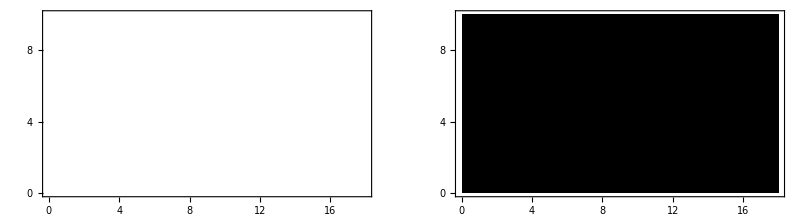

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

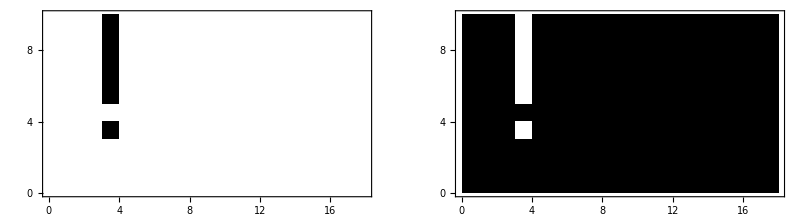

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

General::stop: Further output of GraphicsArray::obs will be suppressed during this calculation.

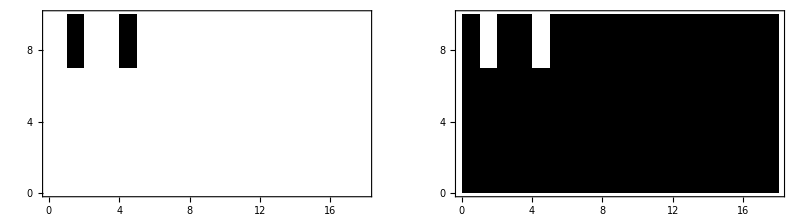

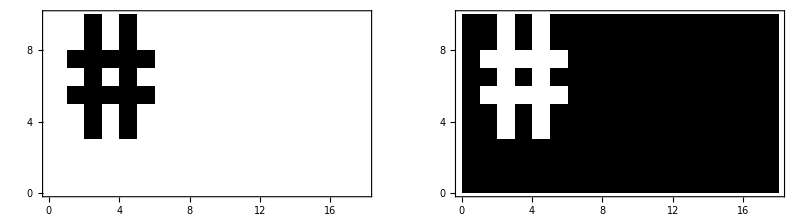

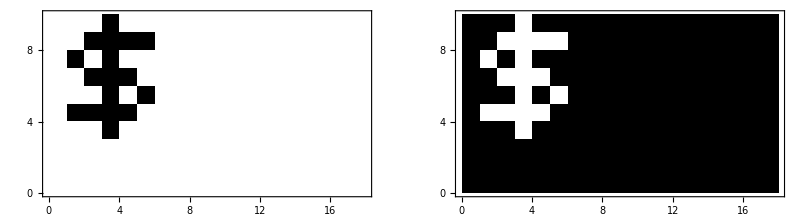

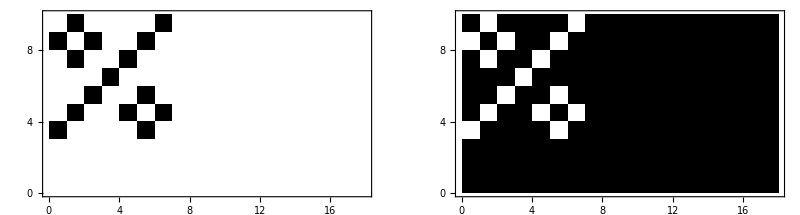

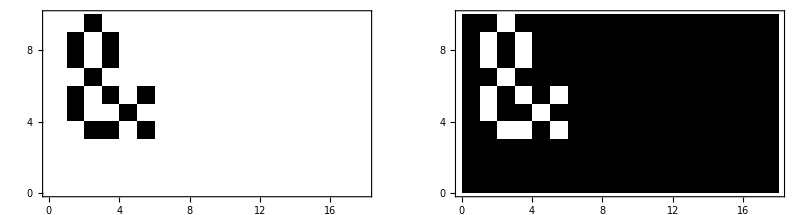

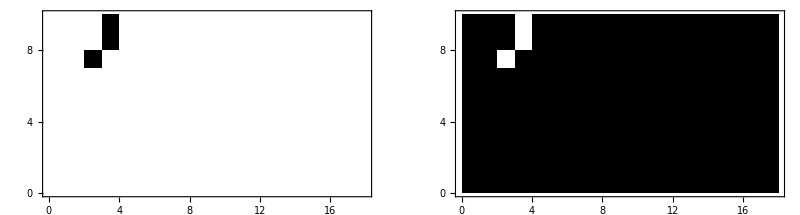

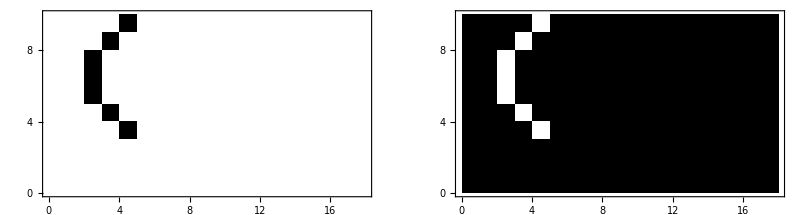

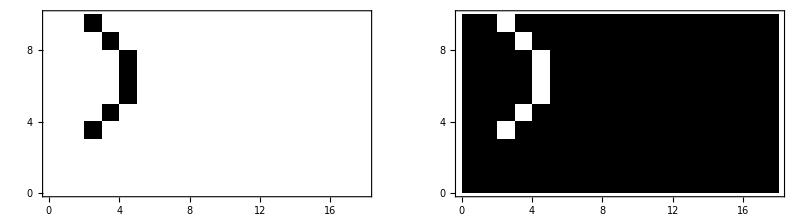

```mathematica
Map[Graphics[Raster[#],Frame->True,AspectRatio->Divide@@Dimensions[#],FrameTicks->({#,#,{},{}}&[Range[0,16,4]])]&,AT320240bitmaps,{2}];
Print[GraphicsArray[#]]&/@%;
```

```mathematica
outputbitmasks=Map[WordBuild,AT320240bitmaps,{-2}];
outputcharsize=MapThread[{Length[First[#1]],#2}&,{AT320240bitmaps,widths}];
outputcharacters=MapThread[Flatten[{#2,#1}]&,{outputbitmasks,outputcharsize}];
Dimensions[outputcharacters]
```

{95,22}

### Organize the font as one contiguous file

```mathematica
offsets=Drop[FoldList[Plus,0,Length/@outputcharacters],-1];
```

```mathematica
TableForm[Join[{"const lcd_primitive experimentalfont[]=","{"},("\texperimentalfont_addr + "<>ToString[#]<>","&/@offsets),{"};"}]]
Export["experimentalfont.c.snippet",%,"Lines"]
```

const lcd_primitive experimentalfont[]=
{
	experimentalfont_addr + 0,
	experimentalfont_addr + 22,
	experimentalfont_addr + 44,
	experimentalfont_addr + 66,
	experimentalfont_addr + 88,
	experimentalfont_addr + 110,
	experimentalfont_addr + 132,
	experimentalfont_addr + 154,
	experimentalfont_addr + 176,
	experimentalfont_addr + 198,
	experimentalfont_addr + 220,
	experimentalfont_addr + 242,
	experimentalfont_addr + 264,
	experimentalfont_addr + 286,
	experimentalfont_addr + 308,
	experimentalfont_addr + 330,
	experimentalfont_addr + 352,
	experimentalfont_addr + 374,
	experimentalfont_addr + 396,
	experimentalfont_addr + 418,
	experimentalfont_addr + 440,
	experimentalfont_addr + 462,
	experimentalfont_addr + 484,
	experimentalfont_addr + 506,
	experimentalfont_addr + 528,
	experimentalfont_addr + 550,
	experimentalfont_addr + 572,
	experimentalfont_addr + 594,
	experimentalfont_addr + 616,
	experimentalfont_addr + 638,
	experimentalfont_addr + 660,
	experimentalfont_addr + 682,
	experimentalfont_addr + 704,
	experimentalfont_addr + 726,
	experimentalfont_addr + 748,
	experimentalfont_addr + 770,
	experimentalfont_addr + 792,
	experimentalfont_addr + 814,
	experimentalfont_addr + 836,
	experimentalfont_addr + 858,
	experimentalfont_addr + 880,
	experimentalfont_addr + 902,
	experimentalfont_addr + 924,
	experimentalfont_addr + 946,
	experimentalfont_addr + 968,
	experimentalfont_addr + 990,
	experimentalfont_addr + 1012,
	experimentalfont_addr + 1034,
	experimentalfont_addr + 1056,
	experimentalfont_addr + 1078,
	experimentalfont_addr + 1100,
	experimentalfont_addr + 1122,
	experimentalfont_addr + 1144,
	experimentalfont_addr + 1166,
	experimentalfont_addr + 1188,
	experimentalfont_addr + 1210,
	experimentalfont_addr + 1232,
	experimentalfont_addr + 1254,
	experimentalfont_addr + 1276,
	experimentalfont_addr + 1298,
	experimentalfont_addr + 1320,
	experimentalfont_addr + 1342,
	experimentalfont_addr + 1364,
	experimentalfont_addr + 1386,
	experimentalfont_addr + 1408,
	experimentalfont_addr + 1430,
	experimentalfont_addr + 1452,
	experimentalfont_addr + 1474,
	experimentalfont_addr + 1496,
	experimentalfont_addr + 1518,
	experimentalfont_addr + 1540,
	experimentalfont_addr + 1562,
	experimentalfont_addr + 1584,
	experimentalfont_addr + 1606,
	experimentalfont_addr + 1628,
	experimentalfont_addr + 1650,
	experimentalfont_addr + 1672,
	experimentalfont_addr + 1694,
	experimentalfont_addr + 1716,
	experimentalfont_addr + 1738,
	experimentalfont_addr + 1760,
	experimentalfont_addr + 1782,
	experimentalfont_addr + 1804,
	experimentalfont_addr + 1826,
	experimentalfont_addr + 1848,
	experimentalfont_addr + 1870,
	experimentalfont_addr + 1892,
	experimentalfont_addr + 1914,
	experimentalfont_addr + 1936,
	experimentalfont_addr + 1958,
	experimentalfont_addr + 1980,
	experimentalfont_addr + 2002,
	experimentalfont_addr + 2024,
	experimentalfont_addr + 2046,
	experimentalfont_addr + 2068,
};

experimentalfont.c.snippet

### Send data function

```mathematica
SaveCharacterFile=Function[{filename,data},
Block[{stream=OpenWrite[filename],headertemplate="1651 1 0 1 "},
Write[stream,OutputForm[#]]&/@
Prepend["0x"<>StringSplit[ToString[BaseForm[#,16]]]⟦1⟧&/@data,headertemplate<>ToString[Length[data]]];
Close[stream]]
]
```

Function[{filename,data},Block[{stream=OpenWrite[filename],headertemplate=1651 1 0 1 },(Write[stream,#1]&)/@Prepend[(0x<>StringSplit[ToString[Slot[1_16]]]⟦1⟧&)/@data,headertemplate<>ToString[Length[data]]];Close[stream]]]

```mathematica
SaveCharacterFile["experimentalfont.dat2",Flatten[outputcharacters]];
```